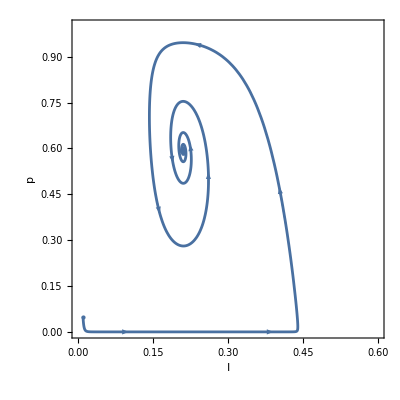

./figures/ita0001.png

```mathematica
(*定义参数和方程*)
ClearAll["Global`*"]
mu=1;                  (*恢复速率*)
be=0.18;                  (*传播速率与接触人数的乘积*)
alp = 0.5;              (*防护效果*)
w=5;                       (*行为更新速率*)
c0=1;                 (*采取防护措施的花费*)
cI=7;               (*被感染后的代价*)
k = 10;
gam = 1;           (*对传播参数的误判，与媒体宣传有关*)
ita = 0.001;             (*社会一致性的影响强度*)

f[x_,y_]:=-mu*x +be*k*(1-alp*y)*(1-x)*x 
g[x_,y_]:=w*y*(1-y)*(-c0+ cI*(Exp[-(1-alp)*be*k*gam*x]-Exp[-be*k*gam*x]) +2*ita*(2*y-1))
sol1 = NDSolve[{x'[t]==-mu*x[t] +be*k*(1-alp*y[t])*(1-x[t])*x[t] ,y'[t]==w*y[t]*(1-y[t])*(-c0+ cI*(Exp[-(1-alp)*be*k*gam*x[t]]-Exp[-be*k*gam*x[t]]) +2*ita*(2*y[t]-1)),x[0]==0.01,y[0]==0.05},{x,y},{t,0,60} ];

img = ParametricPlot[Evaluate[{x[t],y[t]}/. sol1],{t,0,60},PlotRange->{{0,0.6},{0,1}},PlotRangePadding->Scaled[0.03],PlotStyle->{RGBColor[0.285714,0.439024,0.631373],Thickness},Frame->True,AspectRatio->1,FrameLabel->{Style["I",Black, 20],Style["p",Black, 20]},FrameTicksStyle->Directive[FontSize->20,Black],Epilog->{Table[{RGBColor[0.285714,0.439024,0.631373],Arrow[{{x[t],y[t]}/. sol1[[1]],{x[t+0.2],y[t+0.2]}/. sol1[[1]]}]},{t,{3,7,12,14,18,21,26,30}}],{RGBColor[0.285714,0.439024,0.631373],PointSize[Large],Point[{0.01,0.05}]}}]

(*t = Log[r]/((1-r)*(-be))*)
(*绘制向量场*)
(*VectorPlot[{f[x,y],g[x,y]},(*向量场定义*){x,0,1},(*x 的范围*){y,0,1},(*y 的范围*)VectorScale->{Small,Automatic,None},(*箭头大小*)VectorStyle->Arrowheads[0.02],(*箭头样式*)Axes->True,(*显示坐标轴*)Frame->True                            (*显示边框*)]*)
(*img = StreamPlot[{f[x,y],g[x,y]},{x,0,1},{y,0,1},Frame->True,FrameLabel->{Style["I",Black, 20],Style["p",Black, 20]},StreamPoints->Fine,StreamScale-> 0.1,StreamStyle->Thickness,FrameTicksStyle->Directive[FontSize->20,Black],PlotRangePadding->Scaled[0.03], StreamColorFunction->None]*)
SetDirectory[NotebookDirectory[]];
Export["./figures/ita0001.png",img,ImageResolution->400]
```

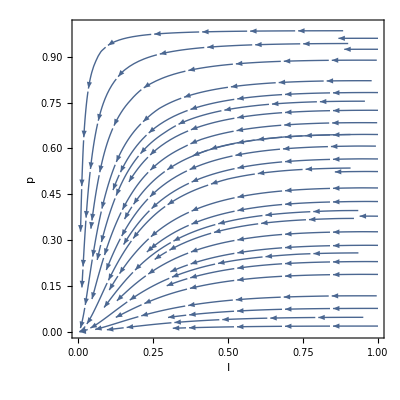

-Graphics-

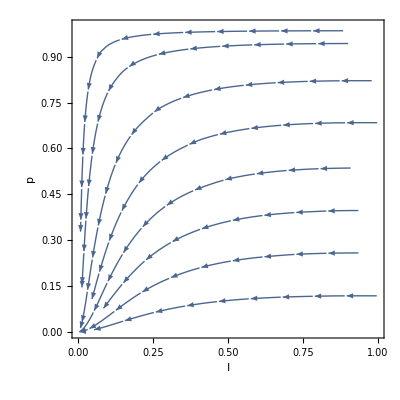

-Graphics-

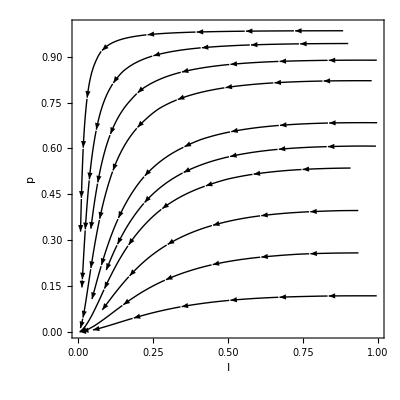

-Graphics-

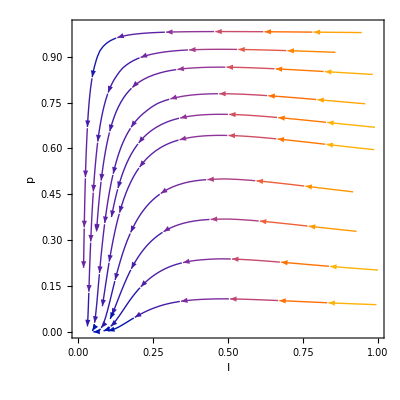

-Graphics-

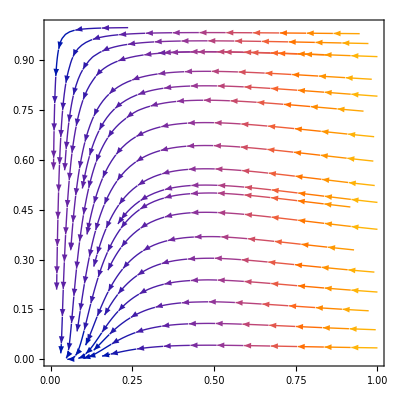

-Graphics-

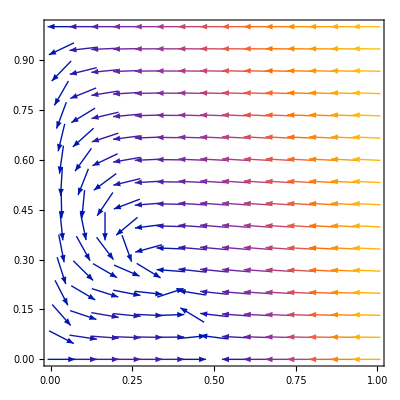

-Graphics-